# 2nd Derivative, 2nd Order CFD, 4/2 Order Filter

## GR Research Group

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
```

## CFD Interior

System:
	P=(1
α
0
0 α
1
α
0 0
α
1
α 0
0
α
1)
Q=(a_0
a_1
0
0 a_1
a_0
a_1
0 0
a_1
a_0
a_1 0
0
a_1
a_0)
Where a_0=-2 a_1.

```mathematica
r=0.8;
```

```mathematica
r=0.8;
fixedPars={α};
freePars={a1,a2,a3};
a2=0;a3=0;
fixed=Solve[1+2 α==2/(2!) a1,fixedPars][[1]]
```

{α→1/2 (-1+a1)}

```mathematica
κTilde[κ_]:=-((-2 a1)+2 a1 Cos[κ])/(1+2 α Cos[κ]);
Δ2[κ_]:=(κ^2*(1+2 α Cos[κ])-(-(-2 a1)+2 a1 Cos[κ]))^2
err=Integrate[Δ2[κ]/.{α->1/2 (-1+a1)},{κ,0,r π}]
coeffs=Solve[{D[err,freePars[[1]]]==0,α==1/2 (-1+a1)},{α,a1}][[1]]
intCoeffs={α->-0.03663613347838532,a1->0.9267277330432293};
```

45.7538-47.5976 a1+25.6805 a1^2

{α→-0.0366361,a1→0.926728}

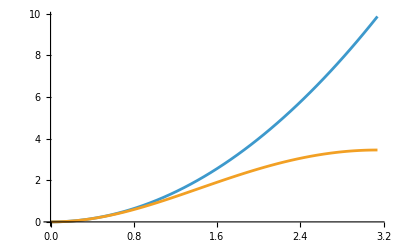

```mathematica
Plot[{κ^2,κTilde[κ]/.coeffs},{κ,0,π}]
```

BD needs b0 through b3 or b4, so maybe we need through a3 or a4??

## CFD Boundary

System:
	P=(1
α
0
0
0 γ
1
α
0
0 0
α
1
α
0 0
0
α
1
γ 0
0
0
α
1)
Q=(b_0
a_1
0
0
0 b_1
a_0
a_1
0
b_3 b_2
a_1
a_0
a_1
b_2 b_3
0
a_1
a_0
b_1 0
0
0
a_1
b_0)
From Taylor expansion, we find:
	b_0+b_1+b_2=0
b_1+2 b_2=0
1/(2!)(b_1+2^2 b_2)=1+γ
1/(3!)(b_1+2^3 b_2)=γ

```mathematica
bdCoeffs=Solve[{b0+b1+b2+b3==0,b1+2 b2+3 b3==0,1/(2!) (b1+2^2 b2+3^2 b3)==1+γ,1/(3!) (b1+2^3 b2+3^3 b3)==γ},{γ,b0,b1,b2,b3}][[1]]

κTildeRe[κ_]:=(-(1+γ Cos[κ]) (b0+b1 Cos[κ]+b2 Cos[2 κ]+b3 Cos[3 κ])-(γ Sin[κ]) (b1 Sin[κ]+b2 Sin[2 κ]+b3 Sin[3 κ]))/((1+γ Cos[κ])^2+(γ Sin[κ])^2);
κTildeIm[κ_]:=((γ Sin[κ]) (b0+b1 Cos[κ]+b2 Cos[2 κ]+b3 Cos[3 κ])-(1+γ Cos[κ]) (b1 Sin[κ]+b2 Sin[2 κ]+b3 Sin[3 κ]))/((1+γ Cos[κ])^2+(γ Sin[κ])^2);
κTildeTot[κ_]:=Abs[κTildeRe[κ]+I κTildeIm[κ]];
ΔTot[κ_]=(κ^2-κTildeTot[κ])^2;
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{b0→2+γ,b1→-5-2 γ,b2→4+γ,b3→-1}

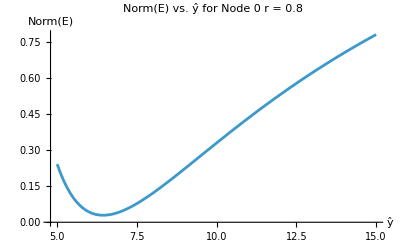

```mathematica
γArray=Range[5,15,0.1];
ΔTotArray=Table[ΔTot[κ]/.bdCoeffs/.{γ->γArray[[i]]},{i,1,Length@γArray}];
errArray=Table[NIntegrate[ΔTotArray[[i]],{κ,0,r π}],{i,1,Length@γArray}];

ListPlot[Transpose@{γArray,errArray},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 0\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]
```

```mathematica
(*γ=-0.6180*)
bdCoeffs/.{γ->0.1}
newbdCoeffs=AppendTo[bdCoeffs/.{γ->6.5},γ->6.5]
```

{b0→2.1,b1→-5.2,b2→4.1,b3→-1}

Set::write: Tag ReplaceAll in {b0→2+γ,b1→-5-2 γ,b2→4+γ,b3→-1}/.{γ→6.5} is Protected.

{b0→8.5,b1→-18.,b2→10.5,b3→-1,γ→6.5}

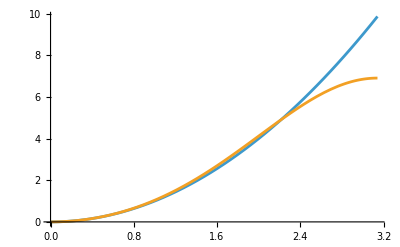

```mathematica
Plot[{κ^2,κTildeRe[κ]/.newbdCoeffs},{κ,0,π}]
```

## Eigenvalues

```mathematica
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
If[i==1&&j==2,γ,
If[i==k&&j==k-1,γ,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
0]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]
LHS[10]//MatrixForm
```

(1 | γ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
α | 1 | α | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | α | 1 | α | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | α | 1 | α | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | α | 1 | α | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | α | 1 | α | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | α | 1 | α | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | α | 1 | α | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | α | 1 | α
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | γ | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
If[i==1&&j==1,(*1+γ*)b0,
If[i==1&&j==2,(*-2 (1+γ)*)b1,
If[i==1&&j==3,(*1+γ*)b2,
If[i==1&&j==4,b3,
If[i==k&&j==k,(*1+γ*)b0,
If[i==k&&j==k-1,(*-2 (1+γ)*)b1,
If[i==k&&j==k-2,(*1+γ*)b2,
If[i==k&&j==k-3,b3,
If[i-1==j,a1,
If[i==j,-2*(a1),
If[i+1==j, a1,
0]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]
RHS[10]//MatrixForm
```

(b0 | b1 | b2 | b3 | 0 | 0 | 0 | 0 | 0 | 0
a1 | -2 a1 | a1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | a1 | -2 a1 | a1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | a1 | -2 a1 | a1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | a1 | -2 a1 | a1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | a1 | -2 a1 | a1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | a1 | -2 a1 | a1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | a1 | -2 a1 | a1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | a1 | -2 a1 | a1
0 | 0 | 0 | 0 | 0 | 0 | b3 | b2 | b1 | b0)

```mathematica
k=40;
g=-1;
(*4th with both fixed: {α->1/10,a1->6/5}*)
LHSNum=(LHS[k]/.coeffs)/.{γ->g};
RHSNum=(RHS[k]/.coeffs)/.{γ->g};

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^1;
Sort[eigs];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->All]
```

$Aborted

Sort::normal: Nonatomic expression expected at position 1 in Sort[eigs].

ComplexListPlot::ldata: eigs is not a valid dataset or list of datasets.

ComplexListPlot[eigs,AspectRatio→1/GoldenRatio,PlotRange→All]

## Filter

```mathematica
Clear["`*"]
```

```mathematica
Clear[g]
```

We have a Taylor series equation for 4th order on the filter interior:
	a_1+2^2 a_2+3^2 a_3=0
We define the transfer function:
	T(κ)=1+(2 ∑_m a_m (cos(m κ)-1))/(1+2 α cos(κ)+2 β cos(2 κ))=1+(2 (a_1 cos(κ)+a_2 cos(2 κ)+a_3 cos(3 κ))-2 (a_1+a_2+a_3))/(1+2 α cos(κ)+2 β cos(2 κ))
We impose the constraints:
	T(π)=0
(d^2 T)/dκ^2(π)=0
We then have:
	T(π)=1+(2 (a_1 cos(π)+a_2 cos(2 π)+a_3 cos(3 π))-2 (a_1+a_2+a_3))/(1+2 α cos(π)+2 β cos(2 π))
=1+(2 (-a_1+a_2-a_3-a_1-a_2-a_3))/(1-2 α+2 β)
=1+(2 (-2 a_1-2 a_3))/(1-2 α+2 β)=0
-4 a_1-4 a_3=-1+2 α-2 β
2 (α-β)+2^2 (a_1+a_3)-1=0
Similarly:
	(d^2 T)/dκ^2(π)=0
α-2^2 β+a_1-2^2 a_2+3^2 a_3=0
Finally, we constrain:
	T(κ_c)=R
with R∈(0,1) and κ_c∈(0,π).

```mathematica
a3=0;

T[κ_]:=1+(2 (a1 Cos[κ]+a2 Cos[2 κ]+a3 Cos[3 κ])-2 (a1+a2+a3))/(1+2 α Cos[κ]+2 β Cos[2 κ])

eqTS=a1+2^2 a2+3^2 a3==0;
eqCr1=2 (α-β)+2^2 (a1+a3)-1==0;
eqCr2=α-2^2 β+a1-2^2 a2+3^2 a3==0;
eqF=(T[κc]==R)/.{R->1/2};

Solve[{eqTS,eqCr1,eqCr2,eqF},{α,β,a1,a2}][[1]]
```

{α→-(8 Cos[κc])/(3 (3+Cos[2 κc])),β→1/6,a1→-(-3-4 Cos[κc]-Cos[2 κc])/(3 (3+Cos[2 κc])),a2→-(3+4 Cos[κc]+Cos[2 κc])/(12 (3+Cos[2 κc]))}

### a_3=0 Case:

Yay! Here’s our interior:

```mathematica
fIntCoeff={α->-(8 Cos[κc])/(3 (3+Cos[2 κc])),β->1/6,a1->-(-3-4 Cos[κc]-Cos[2 κc])/(3 (3+Cos[2 κc])),a2->-(3+4 Cos[κc]+Cos[2 κc])/(12 (3+Cos[2 κc]))};
```

We have the following polynomials:
	g(x^*)=f_0+(∑_(m=1))^2 c_m (x^*)^m
Δ̂ g(x^*)=Δ̂ f_0+(∑_(m=1))^2 d_m (x^*)^m
In this case, our constraint equations are:
	g(m)=f_m  for m=1,2
Δ̂ g(m)=Δ̂ f_m  for m=1,2

More explicitly:
	f_0+c_1+c_2=f_1
f_0+2 c_1+2^2 c_2=f_2
Δ̂ f_0+d_1+d_2=Δ̂ f_1
Δ̂ f_0+2 d_1+2^2 d_2=Δ̂ f_2

```mathematica
extrapEq1=f0+c1+c2==f1;
extrapEq2=f0+2 c1+2^2 c2==f2;
extrapEq3=DHf0+d1+d2==DHf1;
extrapEq4=DHf0+2 d1+2^2 d2==DHf2;

extrapCoeff=Solve[{extrapEq1,extrapEq2,extrapEq3,extrapEq4},{c1,c2,d1,d2}][[1]]

g[x_]:=f0+c1 x+c2 x^2/.extrapCoeff
DHg[x_]:=DHf0+d1 x+d2 x^2/.extrapCoeff
DHg[-2]//FullSimplify
```

{c1→1/2 (-3 f0+4 f1-f2),c2→1/2 (f0-2 f1+f2),d1→1/2 (-3 DHf0+4 DHf1-DHf2),d2→1/2 (DHf0-2 DHf1+DHf2)}

6 DHf0-8 DHf1+3 DHf2

We then have to consider the nodes for i=0, i=1:
	Node 0:
		α Δ̂ g(-1)+Δ̂ f_0+α Δ̂ f_1=(∑_(m=1))^2 a_m (g(-m)-2 f_0+f_m)
	Node 1:
		α Δ̂ f_0+Δ̂ f_1+α Δ̂ f_2=(∑_(m=1))^2 a_m (f/g(1-m)-2 f_1+f_(1+m))
This means that we only have to change the LHS matrix for Node 0, while we have to change the RHS matrix for Node 0, Node 1.

We set these to be in the form:
	Node 0:
		Δ̂ f_0+γ_01 Δ̂ f_1+γ_02 Δ̂ f_2=a_00 f_0+a_01 f_1+a_02 f_2
	Node 1:
		γ_10 Δ̂ f_0+ Δ̂ f_1+γ_12 Δ̂ f_2+γ_13 Δ̂ f_3=a_10 f_0+a_11 f_1+a_12 f_2+a_13 f_3

```mathematica
vars0={DHf0,DHf1,DHf2,f0,f1,f2};
vars1={DHf0,DHf1,DHf2,DHf3,f0,f1,f2,f3};
coeffs0={γ00,γ01,γ02,a00,a01,a02};
coeffs1={γ10,γ11,γ12,γ13,a10,a11,a12,a13};

eqi0=α DHg[-1]+DHf0+α DHf1-(a1 (g[-1]-2 f0+f1)+a2 (g[-2]-2 f0+f2))(*==0*);
eqi1=α DHf0+DHf1+α DHf2-(a1 (f0-2 f1+f2)+a2 (g[-1]-2 f1+f3))(*==0*);

eqBd0=γ00 DHf0+γ01 DHf1+γ02 DHf2-(a00 f0+a01 f1+a02 f2)(*==0*);
eqBd1=γ10 DHf0+γ11 DHf1+γ12 DHf2+γ13 DHf3-(a10 f0+a11 f1+a12 f2+a13 f3)(*==0*);


eq0=Collect[eqi0-eqBd0,vars0];
eq1=Collect[eqi1-eqBd1,vars1];

bdCoeffs0=(Solve[Table[Coefficient[eq0,vars0[[i]]]==0,{i,1,Length@vars0}],coeffs0][[1]])/.fIntCoeff
bdCoeffs1=(Solve[Table[Coefficient[eq1,vars1[[i]]]==0,{i,1,Length@vars1}],coeffs1][[1]])/.fIntCoeff
```

{γ00→1-(8 Cos[κc])/(3+Cos[2 κc]),γ01→(16 Cos[κc])/(3 (3+Cos[2 κc])),γ02→-(8 Cos[κc])/(3 (3+Cos[2 κc])),a00→-(-3-4 Cos[κc]-Cos[2 κc])/(3 (3+Cos[2 κc]))-(3+4 Cos[κc]+Cos[2 κc])/(3 (3+Cos[2 κc])),a01→-2 (-(-3-4 Cos[κc]-Cos[2 κc])/(3 (3+Cos[2 κc]))-(3+4 Cos[κc]+Cos[2 κc])/(3 (3+Cos[2 κc]))),a02→-(-3-4 Cos[κc]-Cos[2 κc])/(3 (3+Cos[2 κc]))-(3+4 Cos[κc]+Cos[2 κc])/(3 (3+Cos[2 κc]))}

{γ10→-(8 Cos[κc])/(3 (3+Cos[2 κc])),γ11→1,γ12→-(8 Cos[κc])/(3 (3+Cos[2 κc])),γ13→0,a10→-(-3-4 Cos[κc]-Cos[2 κc])/(3 (3+Cos[2 κc]))-(3+4 Cos[κc]+Cos[2 κc])/(4 (3+Cos[2 κc])),a11→(2 (-3-4 Cos[κc]-Cos[2 κc]))/(3 (3+Cos[2 κc]))+(5 (3+4 Cos[κc]+Cos[2 κc]))/(12 (3+Cos[2 κc])),a12→-(-3-4 Cos[κc]-Cos[2 κc])/(3 (3+Cos[2 κc]))-(3+4 Cos[κc]+Cos[2 κc])/(12 (3+Cos[2 κc])),a13→-(3+4 Cos[κc]+Cos[2 κc])/(12 (3+Cos[2 κc]))}

```mathematica
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13]
Clear[γ00,γ01,γ02,a00,a01,a02]

{γ11,γ10,γ12,γ13,a10,a11,a12,a13}=1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13}/.bdCoeffs1
{γ00,γ01,γ02,a00,a01,a02}=1/γ00*{γ00,γ01,γ02,a00,a01,a02}/.bdCoeffs0
```

{1,-(8 Cos[κc])/(3 (3+Cos[2 κc])),-(8 Cos[κc])/(3 (3+Cos[2 κc])),0,-(-3-4 Cos[κc]-Cos[2 κc])/(3 (3+Cos[2 κc]))-(3+4 Cos[κc]+Cos[2 κc])/(4 (3+Cos[2 κc])),(2 (-3-4 Cos[κc]-Cos[2 κc]))/(3 (3+Cos[2 κc]))+(5 (3+4 Cos[κc]+Cos[2 κc]))/(12 (3+Cos[2 κc])),-(-3-4 Cos[κc]-Cos[2 κc])/(3 (3+Cos[2 κc]))-(3+4 Cos[κc]+Cos[2 κc])/(12 (3+Cos[2 κc])),-(3+4 Cos[κc]+Cos[2 κc])/(12 (3+Cos[2 κc]))}

{1,(16 Cos[κc])/(3 (3+Cos[2 κc]) (1-(8 Cos[κc])/(3+Cos[2 κc]))),-(8 Cos[κc])/(3 (3+Cos[2 κc]) (1-(8 Cos[κc])/(3+Cos[2 κc]))),(-(-3-4 Cos[κc]-Cos[2 κc])/(3 (3+Cos[2 κc]))-(3+4 Cos[κc]+Cos[2 κc])/(3 (3+Cos[2 κc])))/(1-(8 Cos[κc])/(3+Cos[2 κc])),-(2 (-(-3-4 Cos[κc]-Cos[2 κc])/(3 (3+Cos[2 κc]))-(3+4 Cos[κc]+Cos[2 κc])/(3 (3+Cos[2 κc]))))/(1-(8 Cos[κc])/(3+Cos[2 κc])),(-(-3-4 Cos[κc]-Cos[2 κc])/(3 (3+Cos[2 κc]))-(3+4 Cos[κc]+Cos[2 κc])/(3 (3+Cos[2 κc])))/(1-(8 Cos[κc])/(3+Cos[2 κc]))}

### β=0 Case:

Yay! Here’s our interior:

```mathematica
fIntCoeff={α->-(9 Cos[κc]-Cos[3 κc])/(4 (3+Cos[2 κc])),a3->-1/32,a1->-(-27-36 Cos[κc]-9 Cos[2 κc]+4 Cos[3 κc])/(32 (3+Cos[2 κc])),a2->-(9 Cos[κc]-Cos[3 κc])/(32 (3+Cos[2 κc]))};
```

In this case, our constraint equations are:
	g(m)=f_m  for m=1,2
Δ̂ g(m)=Δ̂ f_m  for m=1
Node -1:
	α Δ̂ g(-2)+Δ̂ g(-1)+α Δ̂ f_0=(∑_(m=1))^3 a_m (g(-1-m)-2 g(-1)+f_(-1+m))
More explicitly:
	f_0+c_1+c_2=f_1
f_0+2 c_1+2^2 c_2=f_2
Δ̂ f_0+d_1+d_2=Δ̂ f_1
α Δ̂ g(-2)+Δ̂ g(-1)+α Δ̂ f_0=a_1 (g(-2)-2 g(-1)+f_0)+a_2 (g(-3)-2 g(-1)+f_1)+a_3 (g(-4)-2 g(-1)+f_2)

```mathematica
extrapEq1=f0+c1+c2==f1;
extrapEq2=f0+2 c1+2^2 c2==f2;
extrapEq3=DHf0+d1+d2==DHf1;
extrapEq4=α (f0-2 d1+2^2 d2)+(f0-d1+d2)+α DHf0==a1 ((f0-2 c1+2^2 c2)-2 (f0-c1+c2)+f0)+a2 ((f0-3 c1+3^2 c2)-2 (f0-c1+c2)+f1)+a3 ((f0-4 c1+4^2 c2)-2 (f0-c1-c2)+f2);

extrapCoeff=Solve[{extrapEq1,extrapEq2,extrapEq3,extrapEq4},{c1,c2,d1,d2}][[1]]

g[x_]:=f0+c1 x+c2 x^2/.extrapCoeff
DHg[x_]:=DHf0+d1 x+d2 x^2/.extrapCoeff
```

{c1→1/2 (-3 f0+4 f1-f2),c2→1/2 (f0-2 f1+f2),d1→-(DHf0-DHf1-f0+a1 f0+4 a2 f0+11 a3 f0-2 a1 f1-8 a2 f1-22 a3 f1+a1 f2+4 a2 f2+11 a3 f2+3 DHf0 α-4 DHf1 α-f0 α)/(2 (1+3 α)),d2→-(DHf0-DHf1+f0-a1 f0-4 a2 f0-11 a3 f0+2 a1 f1+8 a2 f1+22 a3 f1-a1 f2-4 a2 f2-11 a3 f2+3 DHf0 α-2 DHf1 α+f0 α)/(2 (1+3 α))}

We then have to consider the nodes for i=0, i=1, and i=2:
	Node 0:
		α Δ̂ g(-1)+Δ̂ f_0+α Δ̂ f_1=(∑_(m=1))^3 a_m (g(-m)-2 f_0+f_m)
	Node 1:
		α Δ̂ f_0+Δ̂ f_1+α Δ̂ f_2=(∑_(m=1))^3 a_m (f/g(1-m)-2 f_1+f_(1+m))
	Node 2:
		α Δ̂ f_1+Δ̂ f_2+α Δ̂ f_3=(∑_(m=1))^3 a_m (f/g(2-m)-2 f_2+f_(2+m))
This means that we only have to change the LHS matrix for Node 0, while we have to change the RHS matrix for Node 0, Node 1, and Node 2.

TODO: I NEED TO CHECK THAT THIS DERIVATION FOR EQ. 3.5 IN KIM HOLDS THE SAME OR DIFFERENT
We set these to be in the form:
	Node 0:
		Δ̂ f_0+γ_01 Δ̂ f_1+γ_02 Δ̂ f_2=0
	Node 1:
		γ_10 Δ̂ f_0+ Δ̂ f_1+γ_12 Δ̂ f_2+γ_13 Δ̂ f_3=0
	Node 2:
		γ_20 Δ̂ f_0+γ_21 Δ̂ f_1+ Δ̂ f_2+γ_23 Δ̂ f_3+γ_24 Δ̂ f_4=(∑_(m=0))^5 b_(2m) (f_m-f_2)

```mathematica
eqi0=α DHg[-1]+DHf0+α DHf1-(a1 (g[-1]-2 f0+f1)+a2 (g[-2]-2 f0+f2)+a3 (g[-3]-2 f0+f3))==0;
eqi1=α DHf0+DHf1+α DHf2-(a1 (f0-2 f1+f2)+a2 (g[-1]-2 f1+f3)+a3 (g[-2]-2 f1+f4))==0;
eqi2=α DHf1+DHf2+α DHf3-(a1 (f1-2 f2+f3)+a2 (f0-2 f2+f4)+a3 (g[-1]-2 f2+f5))==0;

Collect[eqi0,{DHf0,DHf1,f0,f1,f2,f3}]
Collect[eqi1,{DHf0,DHf1,DHf2,f0,f1,f2,f3,f4}]
Collect[eqi2,{DHf0,DHf1,DHf2,DHf3,f0,f1,f2,f3,f4,f5}]
```

DHf0-a3 f3+f1 (2 a1+8 a2+15 a3-(2 a1 α)/(1+3 α)-(8 a2 α)/(1+3 α)-(22 a3 α)/(1+3 α))+f2 (-a1-4 a2-6 a3+(a1 α)/(1+3 α)+(4 a2 α)/(1+3 α)+(11 a3 α)/(1+3 α))+DHf1 (α-α^2/(1+3 α))+f0 (-a1-4 a2-8 a3+α-α/(1+3 α)+(a1 α)/(1+3 α)+(4 a2 α)/(1+3 α)+(11 a3 α)/(1+3 α)-α^2/(1+3 α))==0

DHf1+(-a1-3 a2-6 a3) f0+(2 a1+5 a2+10 a3) f1+(-a1-a2-3 a3) f2-a2 f3-a3 f4+DHf0 α+DHf2 α==0

DHf2+(-a2-3 a3) f0+(-a1+3 a3) f1+(2 a1+2 a2+a3) f2-a1 f3-a2 f4-a3 f5+DHf1 α+DHf3 α==0

## Testing

### Convergence

### Eigenspectra

We construct R and S

```mathematica
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13]
Clear[γ00,γ01,γ02,a00,a01,a02]
```

```mathematica
LHSRowsF[i_,j_,k_]:=Module[{numBoundaryRows},
If[i==1&&j==2,γ01,
If[i==1&&j==3,γ02,
If[i==k&&j==k-1,γ01,
If[i==k&&j==k-2,γ02,
If[i==2&&j==1,γ10,
If[i==2&&j==3,γ12,
If[i==2&&j==4,γ13,
If[i==k-1&&j==k,γ10,
If[i==k-1&&j==k-2,γ12,
If[i==k-1&&j==k-3,γ13,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
0]]]]]]]]]]]]]]
LHSF[k_]:=Array[LHSRowsF[#1,#2,k]&,{k,k}]
LHSF[10]//MatrixForm
```

(1 | γ01 | γ02 | 0 | 0 | 0 | 0 | 0 | 0 | 0
γ10 | 1 | γ12 | γ13 | 0 | 0 | 0 | 0 | 0 | 0
0 | α | 1 | α | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | α | 1 | α | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | α | 1 | α | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | α | 1 | α | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | α | 1 | α | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | α | 1 | α | 0
0 | 0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

```mathematica
RHSRowsF[i_,j_,k_]:=Module[{numBoundaryRows},
If[i==1&&j==1,a00,
If[i==1&&j==2,a01,
If[i==1&&j==3,a02,
If[i==k&&j==k,a00,
If[i==k&&j==k-1,a01,
If[i==k&&j==k-2,a02,
If[i==2&&j==1,a10,
If[i==2&&j==2,a11,
If[i==2&&j==3,a12,
If[i==2&&j==4,a13,
If[i==k-1&&j==k,a10,
If[i==k-1&&j==k-1,a11,
If[i==k-1&&j==k-2,a12,
If[i==k-1&&j==k-3,a13,
If[i-2==j,a2,
If[i-1==j,a1,
If[i==j,-2*(a1+a2),
If[i+1==j, a1,
If[i+2==j,a2,
0]]]]]]]]]]]]]]]]]]]]
RHSF[k_]:=Array[RHSRowsF[#1,#2,k]&,{k,k}]
RHSF[10]//MatrixForm
```

(a00 | a01 | a02 | 0 | 0 | 0 | 0 | 0 | 0 | 0
a10 | a11 | a12 | a13 | 0 | 0 | 0 | 0 | 0 | 0
a2 | a1 | -2 (a1+a2) | a1 | a2 | 0 | 0 | 0 | 0 | 0
0 | a2 | a1 | -2 (a1+a2) | a1 | a2 | 0 | 0 | 0 | 0
0 | 0 | a2 | a1 | -2 (a1+a2) | a1 | a2 | 0 | 0 | 0
0 | 0 | 0 | a2 | a1 | -2 (a1+a2) | a1 | a2 | 0 | 0
0 | 0 | 0 | 0 | a2 | a1 | -2 (a1+a2) | a1 | a2 | 0
0 | 0 | 0 | 0 | 0 | a2 | a1 | -2 (a1+a2) | a1 | a2
0 | 0 | 0 | 0 | 0 | 0 | a13 | a12 | a11 | a10
0 | 0 | 0 | 0 | 0 | 0 | 0 | a02 | a01 | a00)

```mathematica
Clear[kappac]
```

```mathematica
Clear[kappac]
kappac=0.8 π;

fIntCoeff/.{κc->kappac}//N

Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13]
Clear[γ00,γ01,γ02,a00,a01,a02]

{γ11,γ10,γ12,γ13,a10,a11,a12,a13}=1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13}/.bdCoeffs1/.{κc->kappac}
{γ00,γ01,γ02,a00,a01,a02}=1/γ00*{γ00,γ01,γ02,a00,a01,a02}/.bdCoeffs0/.{κc->kappac}
```

{α→0.65197,β→0.166667,a1→0.00734851,a2→-0.00183713}

{1,0.65197,0.65197,0,0.00183713,-0.00551138,0.00551138,-0.00183713}

{1,-0.44113,0.220565,0.,0.,0.}

```mathematica
a0=-2 (0.0073485083333575205-0.0018371270833393801)
```

-0.0110228

```mathematica
k=6;
Clear[P,Q,R,S]
P=LHS[k];
Q=RHS[k];
R=LHSF[k];
S=RHSF[k]/.fIntCoeff;
mat=Inverse[P].Q.(IdentityMatrix[k]+Inverse[R].S);
CharacteristicPolynomial[mat,λ];
```

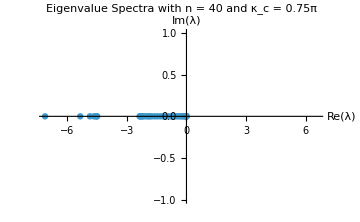
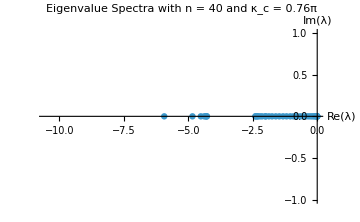
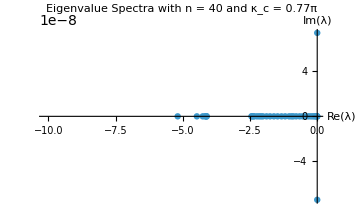
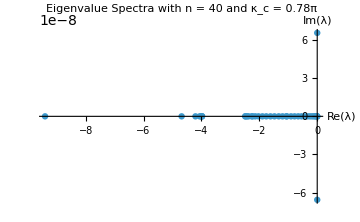
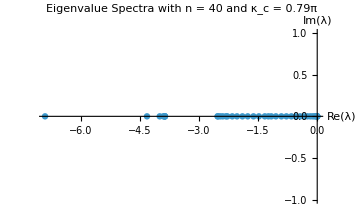
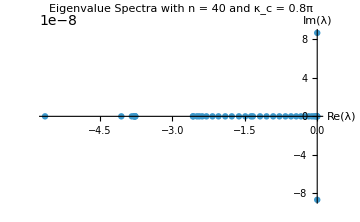
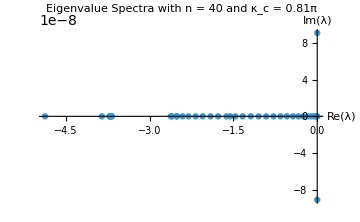
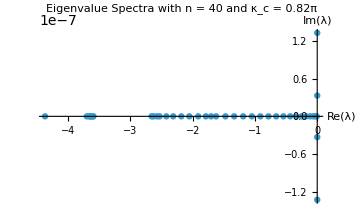

{{20.6304,-7.10367,-5.33572,-4.8518,-4.65128,-4.55524,-4.50731,-4.48488,-2.34934,-2.34649,-2.28801,-2.24922,-2.18769,-2.11857,-1.99721,-1.91229,-1.83986,-1.74348,-1.60172,-1.46766,-1.3233,-1.18714,-1.04518,-0.916686,-0.780836,-0.719062,-0.643399,-0.541479,-0.432067,-0.336932,-0.249599,-0.175583,-0.112984,-0.0641098,-0.028555,-0.00717391,1.12835×10^-7,-1.12835×10^-7,4.95785×10^-8,-4.95783×10^-8},{-95.7999,-5.9336,-4.83913,-4.51531,-4.38154,-4.31962,-4.29034,-4.27747,-2.39759,-2.39019,-2.32028,-2.31,-2.22417,-2.13753,-2.00961,-1.99812,-1.87274,-1.7497,-1.60741,-1.47096,-1.32577,-1.18935,-1.0463,-0.922474,-0.810124,-0.781329,-0.652422,-0.541686,-0.432891,-0.337014,-0.249829,-0.175613,-0.113056,-0.0641189,-0.0285702,-0.00717483,-2.78682×10^-7,2.78681×10^-7,-3.89758×10^-8,3.89754×10^-8},{-16.1754+0. ⅈ,-5.19069+0. ⅈ,-4.47736+0. ⅈ,-4.25893+0. ⅈ,-4.17153+0. ⅈ,-4.13393+0. ⅈ,-4.11812+0. ⅈ,-4.11229+0. ⅈ,-2.44571+0. ⅈ,-2.42995+0. ⅈ,-2.37334+0. ⅈ,-2.34792+0. ⅈ,-2.24742+0. ⅈ,-2.16413+0. ⅈ,-2.09075+0. ⅈ,-2.02001+0. ⅈ,-1.88486+0. ⅈ,-1.75509+0. ⅈ,-1.61178+0. ⅈ,-1.47399+0. ⅈ,-1.32779+0. ⅈ,-1.19215+0. ⅈ,-1.04723+0. ⅈ,-0.958616+0. ⅈ,-0.889197+0. ⅈ,-0.781742+0. ⅈ,-0.655074+0. ⅈ,-0.541859+0. ⅈ,-0.433427+0. ⅈ,-0.337083+0. ⅈ,-0.250007+0. ⅈ,-0.175639+0. ⅈ,-0.113115+0. ⅈ,-0.0641265+0. ⅈ,-0.028583+0. ⅈ,-0.00717561+0. ⅈ,2.05404×10^-14+7.40306×10^-8 ⅈ,2.05404×10^-14-7.40306×10^-8 ⅈ,-6.71261×10^-8+0. ⅈ,6.7126×10^-8+0. ⅈ},{-9.40192+0. ⅈ,-4.68405+0. ⅈ,-4.20595+0. ⅈ,-4.06004+0. ⅈ,-4.00592+0. ⅈ,-3.98609+0. ⅈ,-3.97988+0. ⅈ,-3.97926+0. ⅈ,-2.48973+0. ⅈ,-2.47344+0. ⅈ,-2.42599+0. ⅈ,-2.37285+0. ⅈ,-2.26541+0. ⅈ,-2.2302+0. ⅈ,-2.13945+0. ⅈ,-2.02886+0. ⅈ,-1.89273+0. ⅈ,-1.75981+0. ⅈ,-1.61531+0. ⅈ,-1.47699+0. ⅈ,-1.32947+0. ⅈ,-1.19815+0. ⅈ,-1.06752+0. ⅈ,-1.04801+0. ⅈ,-0.906152+0. ⅈ,-0.782086+0. ⅈ,-0.656349+0. ⅈ,-0.542004+0. ⅈ,-0.433804+0. ⅈ,-0.337141+0. ⅈ,-0.250146+0. ⅈ,-0.175661+0. ⅈ,-0.113164+0. ⅈ,-0.064133+0. ⅈ,-0.0285938+0. ⅈ,-0.00717628+0. ⅈ,1.11968×10^-13+6.56418×10^-8 ⅈ,1.11968×10^-13-6.56418×10^-8 ⅈ,-6.52522×10^-8+0. ⅈ,6.52521×10^-8+0. ⅈ},{-6.91018,-4.3219,-3.99814,-3.90405,-3.87564,-3.873,-3.86643,-3.86555,-2.5294,-2.52317,-2.46332,-2.39861,-2.31638,-2.28028,-2.15686,-2.03646,-1.89879,-1.76406,-1.61821,-1.48063,-1.33087,-1.24011,-1.16565,-1.04866,-0.909753,-0.782374,-0.657115,-0.542124,-0.434081,-0.33719,-0.250257,-0.175679,-0.113204,-0.0641385,-0.0286028,-0.00717684,6.15799×10^-8,-6.15798×10^-8,4.66281×10^-8,-4.66281×10^-8},{-5.63349+0. ⅈ,-4.05463+0. ⅈ,-3.83702+0. ⅈ,-3.78633+0. ⅈ,-3.78222+0. ⅈ,-3.7805+0. ⅈ,-3.76656+0. ⅈ,-3.76464+0. ⅈ,-2.57308+0. ⅈ,-2.56497+0. ⅈ,-2.49091+0. ⅈ,-2.44128+0. ⅈ,-2.38038+0. ⅈ,-2.29281+0. ⅈ,-2.16771+0. ⅈ,-2.04304+0. ⅈ,-1.90367+0. ⅈ,-1.76817+0. ⅈ,-1.62062+0. ⅈ,-1.48886+0. ⅈ,-1.37058+0. ⅈ,-1.33204+0. ⅈ,-1.18344+0. ⅈ,-1.0492+0. ⅈ,-0.911341+0. ⅈ,-0.782612+0. ⅈ,-0.657633+0. ⅈ,-0.542224+0. ⅈ,-0.434293+0. ⅈ,-0.33723+0. ⅈ,-0.250346+0. ⅈ,-0.175694+0. ⅈ,-0.113237+0. ⅈ,-0.0641431+0. ⅈ,-0.0286104+0. ⅈ,-0.00717732+0. ⅈ,1.2153×10^-13+8.67037×10^-8 ⅈ,1.2153×10^-13-8.67037×10^-8 ⅈ,-5.13133×10^-8+0. ⅈ,5.13132×10^-8+0. ⅈ},{-4.8699+0. ⅈ,-3.85313+0. ⅈ,-3.71507+0. ⅈ,-3.71361+0. ⅈ,-3.70516+0. ⅈ,-3.69673+0. ⅈ,-3.67761+0. ⅈ,-3.6752+0. ⅈ,-2.61895+0. ⅈ,-2.59738+0. ⅈ,-2.51308+0. ⅈ,-2.50972+0. ⅈ,-2.40796+0. ⅈ,-2.30344+0. ⅈ,-2.17598+0. ⅈ,-2.04888+0. ⅈ,-1.90768+0. ⅈ,-1.77319+0. ⅈ,-1.62261+0. ⅈ,-1.55761+0. ⅈ,-1.46286+0. ⅈ,-1.33301+0. ⅈ,-1.18707+0. ⅈ,-1.04965+0. ⅈ,-0.912276+0. ⅈ,-0.78281+0. ⅈ,-0.658005+0. ⅈ,-0.542307+0. ⅈ,-0.434456+0. ⅈ,-0.337263+0. ⅈ,-0.250417+0. ⅈ,-0.175707+0. ⅈ,-0.113264+0. ⅈ,-0.0641469+0. ⅈ,-0.0286167+0. ⅈ,-0.00717772+0. ⅈ,2.75733×10^-14+9.08551×10^-8 ⅈ,2.75733×10^-14-9.08551×10^-8 ⅈ,5.06926×10^-8+0. ⅈ,-5.06926×10^-8+0. ⅈ},{-4.37117+0. ⅈ,-3.6995+0. ⅈ,-3.6575+0. ⅈ,-3.64797+0. ⅈ,-3.6323+0. ⅈ,-3.62087+0. ⅈ,-3.59864+0. ⅈ,-3.59619+0. ⅈ,-2.65955+0. ⅈ,-2.6298+0. ⅈ,-2.57534+0. ⅈ,-2.53146+0. ⅈ,-2.42356+0. ⅈ,-2.31252+0. ⅈ,-2.18263+0. ⅈ,-2.05446+0. ⅈ,-1.91098+0. ⅈ,-1.78829+0. ⅈ,-1.70423+0. ⅈ,-1.62426+0. ⅈ,-1.47438+0. ⅈ,-1.33381+0. ⅈ,-1.18875+0. ⅈ,-1.05002+0. ⅈ,-0.912906+0. ⅈ,-0.782973+0. ⅈ,-0.658284+0. ⅈ,-0.542375+0. ⅈ,-0.434585+0. ⅈ,-0.337291+0. ⅈ,-0.250475+0. ⅈ,-0.175717+0. ⅈ,-0.113287+0. ⅈ,-0.0641501+0. ⅈ,-0.0286219+0. ⅈ,-0.00717805+0. ⅈ,4.03784×10^-14+1.33185×10^-7 ⅈ,4.03784×10^-14-1.33185×10^-7 ⅈ,2.43562×10^-14+3.31862×10^-8 ⅈ,2.43562×10^-14-3.31862×10^-8 ⅈ},{-4.02719,-3.61117,-3.59968,-3.58767,-3.57517,-3.56077,-3.53055,-3.52351,-2.69473,-2.6711,-2.62141,-2.54683,-2.43511,-2.32045,-2.18803,-2.06173,-1.91369,-1.90014,-1.76235,-1.62561,-1.47752,-1.33446,-1.18979,-1.05033,-0.91336,-0.783107,-0.658498,-0.542431,-0.434687,-0.337313,-0.250522,-0.175726,-0.113305,-0.0641528,-0.0286262,-0.00717833,9.55226×10^-8,-9.55222×10^-8,-7.08694×10^-8,7.08693×10^-8},{-3.78163,-3.57347,-3.56081,-3.54149,-3.51498,-3.49748,-3.46945,-3.46113,-2.72469,-2.72027,-2.64782,-2.55973,-2.44423,-2.32799,-2.19242,-2.09899,-2.03087,-1.9159,-1.76908,-1.62672,-1.47919,-1.335,-1.1905,-1.05057,-0.9137,-0.783216,-0.658663,-0.542477,-0.434767,-0.337332,-0.250559,-0.175733,-0.11332,-0.0641549,-0.0286298,-0.00717856,-5.4968×10^-8,5.49677×10^-8,-2.99458×10^-8,2.99457×10^-8},{-3.60299+0. ⅈ,-3.5433+0. ⅈ,-3.52951+0. ⅈ,-3.50834+0. ⅈ,-3.47854+0. ⅈ,-3.4489+0. ⅈ,-3.41098+0. ⅈ,-3.40529+0. ⅈ,-2.76635+0. ⅈ,-2.74984+0. ⅈ,-2.66576+0. ⅈ,-2.57073+0. ⅈ,-2.45152+0. ⅈ,-2.33909+0. ⅈ,-2.23553+0. ⅈ,-2.19596+0. ⅈ,-2.05395+0. ⅈ,-1.91769+0. ⅈ,-1.77181+0. ⅈ,-1.62761+0. ⅈ,-1.4803+0. ⅈ,-1.33543+0. ⅈ,-1.19103+0. ⅈ,-1.05077+0. ⅈ,-0.913959+0. ⅈ,-0.783304+0. ⅈ,-0.658792+0. ⅈ,-0.542514+0. ⅈ,-0.434831+0. ⅈ,-0.337346+0. ⅈ,-0.250589+0. ⅈ,-0.175739+0. ⅈ,-0.113332+0. ⅈ,-0.0641567+0. ⅈ,-0.0286326+0. ⅈ,-0.00717874+0. ⅈ,-9.41705×10^-9+4.14901×10^-8 ⅈ,-9.41705×10^-9-4.14901×10^-8 ⅈ,9.41691×10^-9+4.149×10^-8 ⅈ,9.41691×10^-9-4.149×10^-8 ⅈ},{-3.51929+0. ⅈ,-3.50578+0. ⅈ,-3.48217+0. ⅈ,-3.47356+0. ⅈ,-3.44682+0. ⅈ,-3.41503+0. ⅈ,-3.37038+0. ⅈ,-3.35082+0. ⅈ,-2.80592+0. ⅈ,-2.77072+0. ⅈ,-2.67937+0. ⅈ,-2.58091+0. ⅈ,-2.45733+0. ⅈ,-2.40711+0. ⅈ,-2.32014+0. ⅈ,-2.19881+0. ⅈ,-2.05871+0. ⅈ,-1.91912+0. ⅈ,-1.77349+0. ⅈ,-1.62833+0. ⅈ,-1.48109+0. ⅈ,-1.33578+0. ⅈ,-1.19142+0. ⅈ,-1.05094+0. ⅈ,-0.914158+0. ⅈ,-0.783374+0. ⅈ,-0.658892+0. ⅈ,-0.542543+0. ⅈ,-0.434881+0. ⅈ,-0.337358+0. ⅈ,-0.250613+0. ⅈ,-0.175743+0. ⅈ,-0.113342+0. ⅈ,-0.0641581+0. ⅈ,-0.0286349+0. ⅈ,-0.00717889+0. ⅈ,-1.77005×10^-15+4.61481×10^-8 ⅈ,-1.77005×10^-15-4.61481×10^-8 ⅈ,-7.27718×10^-14+2.44726×10^-8 ⅈ,-7.27718×10^-14-2.44726×10^-8 ⅈ},{-3.50039,-3.48586,-3.46164,-3.43019,-3.38924,-3.37504,-3.33395,-3.30799,-2.83864,-2.78799,-2.68993,-2.59656,-2.52692,-2.46193,-2.33126,-2.20106,-2.06129,-1.92026,-1.77466,-1.6289,-1.48168,-1.33606,-1.19172,-1.05106,-0.91431,-0.783429,-0.65897,-0.542566,-0.43492,-0.337368,-0.250632,-0.175747,-0.113349,-0.0641592,-0.0286368,-0.00717901,-4.58996×10^-8,4.58996×10^-8,3.39955×10^-8,-3.39954×10^-8},{-3.48571+0. ⅈ,-3.47068+0. ⅈ,-3.44572+0. ⅈ,-3.41213+0. ⅈ,-3.36948+0. ⅈ,-3.32776+0. ⅈ,-3.28469+0. ⅈ,-3.27504+0. ⅈ,-2.86495+0. ⅈ,-2.80274+0. ⅈ,-2.69812+0. ⅈ,-2.66635+0. ⅈ,-2.57878+0. ⅈ,-2.46551+0. ⅈ,-2.33548+0. ⅈ,-2.20281+0. ⅈ,-2.06303+0. ⅈ,-1.92114+0. ⅈ,-1.77552+0. ⅈ,-1.62934+0. ⅈ,-1.48212+0. ⅈ,-1.33627+0. ⅈ,-1.19195+0. ⅈ,-1.05116+0. ⅈ,-0.914426+0. ⅈ,-0.783473+0. ⅈ,-0.659029+0. ⅈ,-0.542584+0. ⅈ,-0.43495+0. ⅈ,-0.337375+0. ⅈ,-0.250646+0. ⅈ,-0.17575+0. ⅈ,-0.113355+0. ⅈ,-0.0641601+0. ⅈ,-0.0286382+0. ⅈ,-0.0071791+0. ⅈ,-6.32713×10^-8+0. ⅈ,6.32713×10^-8+0. ⅈ,-1.68966×10^-14+4.42785×10^-8 ⅈ,-1.68966×10^-14-4.42785×10^-8 ⅈ},{-3.47448+0. ⅈ,-3.4591+0. ⅈ,-3.43356+0. ⅈ,-3.39874+0. ⅈ,-3.3545+0. ⅈ,-3.30579+0. ⅈ,-3.25012+0. ⅈ,-3.23439+0. ⅈ,-2.88555+0. ⅈ,-2.8187+0. ⅈ,-2.75506+0. ⅈ,-2.70438+0. ⅈ,-2.58791+0. ⅈ,-2.46826+0. ⅈ,-2.3381+0. ⅈ,-2.20416+0. ⅈ,-2.06427+0. ⅈ,-1.92182+0. ⅈ,-1.77615+0. ⅈ,-1.62968+0. ⅈ,-1.48244+0. ⅈ,-1.33643+0. ⅈ,-1.19212+0. ⅈ,-1.05124+0. ⅈ,-0.914514+0. ⅈ,-0.783506+0. ⅈ,-0.659074+0. ⅈ,-0.542598+0. ⅈ,-0.434973+0. ⅈ,-0.337381+0. ⅈ,-0.250657+0. ⅈ,-0.175752+0. ⅈ,-0.11336+0. ⅈ,-0.0641608+0. ⅈ,-0.0286393+0. ⅈ,-0.00717917+0. ⅈ,-1.29842×10^-7+0. ⅈ,1.29842×10^-7+0. ⅈ,-8.88101×10^-16+6.32663×10^-8 ⅈ,-8.88101×10^-16-6.32663×10^-8 ⅈ},{-3.46607+0. ⅈ,-3.45043+0. ⅈ,-3.42447+0. ⅈ,-3.38879+0. ⅈ,-3.34335+0. ⅈ,-3.29123+0. ⅈ,-3.23166+0. ⅈ,-3.19585+0. ⅈ,-2.90123+0. ⅈ,-2.85667+0. ⅈ,-2.80373+0. ⅈ,-2.70907+0. ⅈ,-2.59233+0. ⅈ,-2.47032+0. ⅈ,-2.33991+0. ⅈ,-2.20517+0. ⅈ,-2.06516+0. ⅈ,-1.92233+0. ⅈ,-1.77662+0. ⅈ,-1.62994+0. ⅈ,-1.48269+0. ⅈ,-1.33656+0. ⅈ,-1.19225+0. ⅈ,-1.05129+0. ⅈ,-0.91458+0. ⅈ,-0.783531+0. ⅈ,-0.659108+0. ⅈ,-0.542608+0. ⅈ,-0.434991+0. ⅈ,-0.337385+0. ⅈ,-0.250666+0. ⅈ,-0.175753+0. ⅈ,-0.113363+0. ⅈ,-0.0641613+0. ⅈ,-0.0286401+0. ⅈ,-0.00717922+0. ⅈ,6.15221×10^-8+0. ⅈ,-6.15217×10^-8+0. ⅈ,1.3409×10^-14+5.86039×10^-8 ⅈ,1.3409×10^-14-5.86039×10^-8 ⅈ}}

```mathematica
k=40;
eigsList={};
Table[
(*kappac=0.8 π;*)
P=(LHS[k]/.intCoeffs)/.newbdCoeffs;
Q=(RHS[k]/.intCoeffs)/.newbdCoeffs;
R=(LHSF[k]/.fIntCoeff)/.{κc->kappac};
S=(RHSF[k]/.fIntCoeff)/.{κc->kappac};
mat=Inverse[P].Q.(IdentityMatrix[k]+Inverse[R].S);
eigs=Eigenvalues[mat];
AppendTo[eigsList,eigs];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","κ_c = ",ToString[kappac/π],"π"],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium]
,{kappac,0.75 π,0.9 π,0.01 π}
]
eigsList
```

Next steps:
	Find BD coeffs, create R and S
	Convergence test comparing Filter 1 and Filter 2?
	Test and compare eigenspectra of P^-1 Q(𝕀+σ R^-1 S)
	
	if we go to 3rd order, we need a 2nd boundary row